```mathematica
;
```

Last updated:   Thu 17 Aug 2023

## General

```mathematica
url="https://notes.msdogo.com/";
```

```mathematica
Once@WolframAlpha@url
```

WolframAlphaQueryResults

## URLs

```mathematica
(* home & meta pages *)
homeURL=URL@url;
metaURL=URL[url<>"meta"];
```

```mathematica
(* snapshots of home & meta pages *)
```

-Graphics--Graphics-

```mathematica
(* collage of homepage images (none at the moment) *)
(*ResourceFunction["WebPageImageCollage"]@homeURL⟦1⟧*)
```

```mathematica
(* check hyperlinks on homepage *)
hyperlinkDS=Once@;
hyperlinkDS=Once[/@hyperlinkDS];
```

https://msdogo.com/ | https://notes.msdogo.com/meta
https://notes.msdogo.com/ | https://notes.msdogo.com/poems-by-adrienne-rich
https://notes.msdogo.com/about | https://notes.msdogo.com/silence
https://notes.msdogo.com/dynamic | https://notes.msdogo.com/wolfram-notebooks
https://notes.msdogo.com/explanations | https://www.algolia.com/?utm_source=react-instantsearch&utm_medium=website&utm_content&utm_campaign=poweredby
https://notes.msdogo.com/historical-perspective |

## Graphs

### External links

```mathematica
(* func for highlighting longest path(s) in a graph *)
highlightLongestPaths@graph_:=;
```

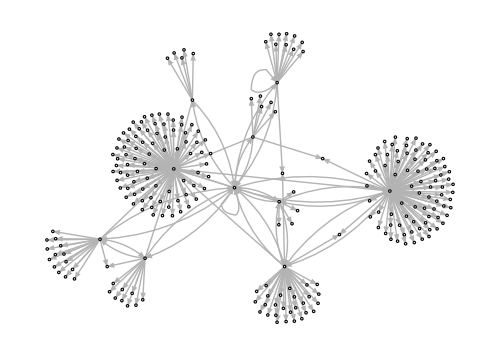

```mathematica
(* level-2 nested graph incl. external links; homePage===aboutPage ∴ ./ ⟦2⟧ w/ ⟦1⟧ *)
gExt=Once@With[{home=url},NestGraph[DeleteDuplicatesBy[StringSplit[#1,"/"]&][DeleteCases[Interpreter["URL"|"URLString"]/@Import[#1,"Hyperlinks"]/.{home|home<>"about"->StringDrop[home,-1]},s_/;StringContainsQ[s,"mail"|"twitter"]||StringContainsQ[s,home~~a__~~"/"~~a__]||StringContainsQ[s,home~~a__~~"/about"]]]&,StringDrop[home,-1],2,VertexLabels->Placed["Name",Tooltip],PlotTheme->"Monochrome",EdgeShapeFunction->GraphElementData["ShortUnfilledArrow","ArrowSize"->0.02],VertexSize->{"Scaled",0.005},DirectedEdges->True,ImageSize->500]]
```

```mathematica
(* longest paths (incl. external links) *)
highlightLongestPaths@gExt
```

notes.msdogo.com/poems-by-adrienne-rich→ « 4 nodes » →notes.msdogo.com/dynamic
-Graphics-
Go to path URL »https://notes.msdogo.com/poems-by-adrienne-rich?stackedPages=%2Fsilence&stackedPages=%2Fabout&stackedPages=%2Fwolfram-notebooks&stackedPages=%2Fmeta&stackedPages=%2FdynamicNonehttps://notes.msdogo.com/poems-by-adrienne-rich?stackedPages=%2Fsilence&stackedPages=%2Fabout&stackedPages=%2Fwolfram-notebooks&stackedPages=%2Fmeta&stackedPages=%2FdynamicHyperlink1
There are 2879 other possible paths.

### Internal links

```mathematica
(* level-3 nested graph (internal links only) *)
gInt=
(*method 2: *)
```

-Graphics-

```mathematica
(* longest paths (internal links only) *)
(* [this is a really inefficient way to this — computation gets exponentially larger as no. of nodes increase!!!] *)
(* try FindLongestPath — https://resources.wolframcloud.com/FunctionRepository/resources/FindLongestPath *)
highlightLongestPaths[gInt]
```

notes.msdogo.com/listening→ « 13 nodes » →notes.msdogo.com/historical-perspective/books
-Graphics-
Go to path URL »https://notes.msdogo.com/listening?stackedPages=%2Fsilence&stackedPages=%2Fadrienne-rich&stackedPages=%2Fpoems-by-adrienne-rich&stackedPages=%2Fbooks&stackedPages=%2Fsmall-is-beautiful&stackedPages=%2Fabout&stackedPages=%2Fdynamic&stackedPages=%2Fmeta&stackedPages=%2Fnote-taking&stackedPages=%2Fwolfram-notebooks&stackedPages=%2Fart&stackedPages=%2Fexploration&stackedPages=%2Fhistorical-perspective&stackedPages=%2FbooksNonehttps://notes.msdogo.com/listening?stackedPages=%2Fsilence&stackedPages=%2Fadrienne-rich&stackedPages=%2Fpoems-by-adrienne-rich&stackedPages=%2Fbooks&stackedPages=%2Fsmall-is-beautiful&stackedPages=%2Fabout&stackedPages=%2Fdynamic&stackedPages=%2Fmeta&stackedPages=%2Fnote-taking&stackedPages=%2Fwolfram-notebooks&stackedPages=%2Fart&stackedPages=%2Fexploration&stackedPages=%2Fhistorical-perspective&stackedPages=%2FbooksHyperlink1
There are 215 other possible paths.

```mathematica
(* connected components *)
```

-Graphics-

```mathematica
(* communities *)
CommunityGraphPlot[gInt,FindGraphCommunities[gInt]]
```

-Graphics-

```mathematica
plotOpts=;
HighlightGraphProperty[g_,prop_,opts___]:=;
```

```mathematica
(* vertex degree *)
HighlightGraphProperty[gInt,VertexDegree]
```

VertexDegree
https://notes.msdogo.com | 30.
https://notes.msdogo.com/wolfram-notebooks | 21.
https://notes.msdogo.com/poems-by-adrienne-rich | 12.
https://notes.msdogo.com/silence | 12.
https://notes.msdogo.com/exploration | 11.
-Graphics-

```mathematica
(* betweenness centrality *)
HighlightGraphProperty[gInt,BetweennessCentrality]
```

BetweennessCentrality
https://notes.msdogo.com | 464.
https://notes.msdogo.com/wolfram-notebooks | 285.2
https://notes.msdogo.com/poems-by-adrienne-rich | 117.2
https://notes.msdogo.com/silence | 103.7
https://notes.msdogo.com/exploration | 95.3
-Graphics-

```mathematica
(* k-core components *)
```

```mathematica
(* independent vertex & edge sets *)
```

{-Graphics-,-Graphics-}

```mathematica
(* vertex & edge covers *)
```

{-Graphics-,-Graphics-}

```mathematica
(* cliques *)
```

-Graphics-

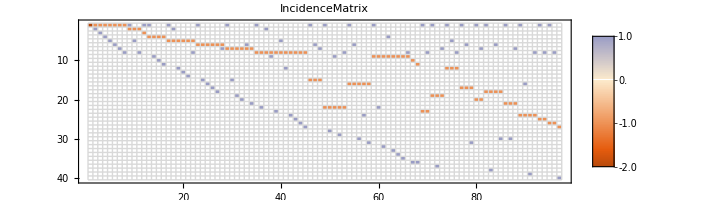
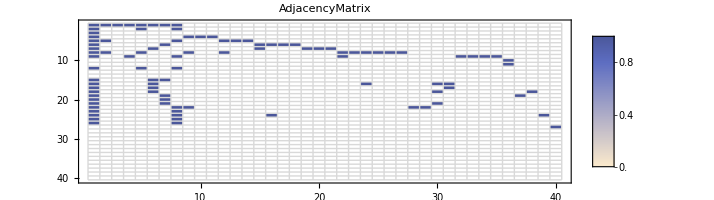
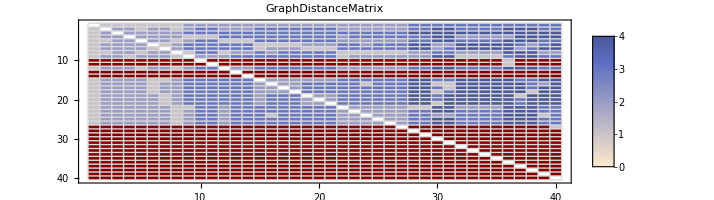

```mathematica
(* grpah matrices *)
```